```mathematica
SetDirectory[NotebookDirectory[]];
Get[FileNameJoin[{Directory[],"HexaBoxModules.m"}]];
PureIntegrals=ReadList[FileNameJoin[{NotebookDirectory[],"files/PureIntegralBasisP1.txt"}]];

$P=2^31-1;
samplepoint=1
SubReduList=Get[ToString[StringForm["``/KIRA/splitres/phasespace_``.m",Directory[],IntegerString[samplepoint,10,5]]]];
tPoint=Thread[Rule[invariants,SubReduList[[2,1]]]];

reductionRules=ReductionRules=GetReductionTableFromList[SubReduList[[2,2]]];

PureIntegralN=Expand[PureIntegrals/.tPoint/.root[n_]:>PowerMod[n,1/2,$P],Modulus->$P];
epsrepl={(ep->(4-d)/2)/.tPoint};

ExtraRelations=GetExtraRelationReplacements[reductionRules,tPoint];
PureIntegralN2=Expand[PureIntegralN/.reductionRules,Modulus->$P];
PureIntegralN3=Expand[PureIntegralN2/.ExtraRelations,Modulus->$P];

NonZeros=Cases[reductionRules,_hxb,Infinity]//DeleteDuplicates;
ZeroInts=Complement[Ureduce,NonZeros];
ZeroIntsRepl=Thread[Rule[ZeroInts,0]];
PureIntegralN4=Expand[PureIntegralN3/.ExtraRelations/.ZeroIntsRepl,Modulus->$P];
SubLaporta=Cases[PureIntegralN4,_hxb,Infinity]//DeleteDuplicates;
PureIntegralN4=Expand[PureIntegralN4/.epsrepl,Modulus->$P];
```

1

```mathematica
SubLaporta;
RemainingInts=Complement[LaportaBasis,SubLaporta];
PureIntegrals2=Join[PureIntegrals,RemainingInts];
Export[FileNameJoin[{NotebookDirectory[],"files/PureIntegralBasisFull.txt"}],PureIntegrals2];
```

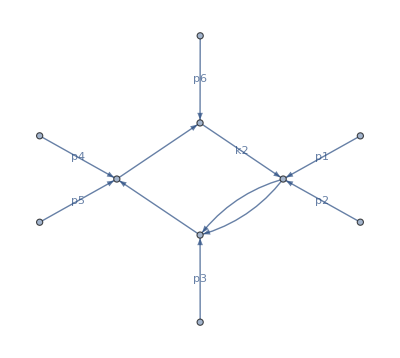

```mathematica
plotDiagram[hxb[-1,0,1,1,0,1,0,1,1,0,0,0,0]]
```